### Equilibrium & Eigenvalues

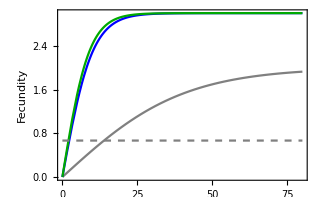
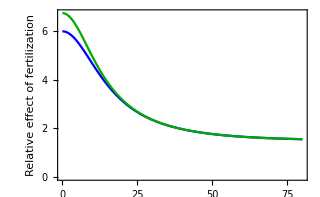
(a)

-Graphics-

(b)

-Graphics-
        Species ordered by competitiveness

```mathematica
Remove["Global`*"];
Clear["Global`*"];

q=0.3;
m=0.2;

frmopt[col_,fsize_]:={Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->Directive[{col,FontFamily->"Times New Roman",FontSize->fsize}]};
fstylopt[txt_,fsize_]:=Style[txt,Black,FontFamily->"Times New Roman",FontSize->fsize]

ino=80;

f0[i_]:=2((1-Exp[-4 i/ino])/(1+Exp[-4 i/ino]));
f1[i_]:=3((1-Exp[-16 i/ino])/(1+Exp[-16 i/ino]));
f2[i_]:=3((1-Exp[-18 i/ino])/(1+Exp[-18 i/ino]));

g0=Plot[m/q,{i,0,ino},PlotStyle->{Gray,Dashed},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Fecundity",14]},ImageSize->320];
g1=Plot[{f0[i],f1[i],f2[i]},{i,0,ino},PlotStyle->{Gray,Blue,Darker[Green]},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Fecundity",14]},ImageSize->320];
g2=Plot[{f1[i]/f0[i],f2[i]/f0[i]},{i,0,ino},PlotStyle->{Blue,Darker[Green]},PlotRange->{0,Automatic},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Relative effect of fertilization",14]},ImageSize->320];

g3=Column[{
fstylopt["(a)",16],Spacer[{0,0}],Show[g1,g0],Spacer[{0,0}],
fstylopt["(b)",16],Spacer[{0,0}],g2,
Item[Style["        Species ordered by competitiveness",Black,FontFamily->"Times New Roman",FontSize->14],Alignment->Center]
},Alignment->Left];

Print[g3];
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_tradeoff.pdf"],g3];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

```mathematica
numeriana[ftype_]:=Do[

q=0.3;
m=0.2;
η = m/q;

Switch[ftype,
1,f[i_]:=f1[i],
2,f[i_]:=f2[i],
_,f[i_]:=f0[i]
];

For[i=1,i≤ino,i++,
Subscript[d0, i]=(q f[i](1-∑_(j=1)^i Subscript[pn, j])-q ∑_(j=1)^(i-1) Subscript[pn, j] f[j]-m)Subscript[pn, i];
];

Subscript[sp, 0]=0;
Subscript[spf, 0]=0;
For[i=1,i≤ino,i++,
If[f[i]≤η ,Subscript[pp, i]=0,Subscript[pp, i]=1-Subscript[sp, i-1]-1/f[i](η+Subscript[spf, i-1])];
If[Subscript[pp, i]<0,Subscript[pp, i]=0];
Subscript[sp, i]=Subscript[sp, i-1]+Subscript[pp, i];
Subscript[spf, i]=Subscript[spf, i-1]+Subscript[pp, i] f[i];
];
];
```

```mathematica
numeriana[0];
inita=Table[{i,Subscript[pp, i]},{i,1,ino}];

inifredis=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@inita},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];

numeriana[1];
endta1=Table[{i,Subscript[pp, i]},{i,1,ino}];

endfredis[1]=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@endta1},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];

numeriana[2];
endta2=Table[{i,Subscript[pp, i]},{i,1,ino}];

endfredis[2]=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@endta2},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];
```

### Simulation

#### NDSovle with Default precision q = 0.3, m =0. 2, n = 80, tmax = 500,000 (if error occurs during calculation, try to decrease “tmin0”)

```mathematica
calc[q_,m_,tminc_,tmaxc_,tc_]:=Do[
pinit=Table[inita[[i]][[2]],{i,1,ino}];
tpinit=Total[pinit];
If[tpinit>1,pinit=pinit/tpinit];

pinit=Table[inita[[i]][[2]],{i,1,ino}];

immig=10^-10;

f[i_]:=f0[i];
ps0=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][0]==pinit[[i]],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tminc,tc}
];

f[i_]:=f1[i];
ps1=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][tc]==ps0[[i]][tc],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tc,tmaxc}
];

f[i_]:=f2[i];
ps2=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][tc]==ps0[[i]][tc],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tc,tmaxc}
];

Print["NDSolve finished!"];
];
```

```mathematica
pscale=0.04;

psampleno=400;
frameopt={FrameStyle->Thickness[0.002],FrameTicksStyle->Directive[{Black,FontFamily->"Times New Roman",FontSize->12}]};

gdraw[tmin_,tmax_,tc_]:=Do[

If[j==1,
dta0=Table[Table[N[If[τ<tc,ps0[[i]][τ],ps1[[i]][τ]],$MachinePrecision],{i,1,ino}],{τ,tmin,tmax,(tmax-tmin)/psampleno}],
dta0=Table[Table[N[If[τ<tc,ps0[[i]][τ],ps2[[i]][τ]],$MachinePrecision],{i,1,ino}],{τ,tmin,tmax,(tmax-tmin)/psampleno}]
];
Print["Type ",j,": Data extraction finished!"];

plt1=ListPlot[Table[Table[{∑_(j=1)^i dta0[[τ]][[j]],tmin+(τ-1)(tmax-tmin)/psampleno},{τ,1,psampleno+1}],{i,1,ino}],Joined->True,PlotRange->{{0.00000001,0.75},Automatic},Frame->True,Evaluate[frameopt],AspectRatio->1.2,ImageSize->{Automatic,250},PlotRangePadding->None];
plt2=ListPlot[Table[Table[{tmin+(τ-1)(tmax-tmin)/psampleno,∑_(j=1)^i dta0[[τ]][[j]]},{τ,1,psampleno+1}],{i,ino,ino}],Joined->True,PlotRange->{Automatic,{0.00000001,0.75}},Frame->True,Evaluate[frameopt],AspectRatio->1.2,ImageSize->{Automatic,250},PlotRangePadding->None,Filling->Top];
(* change a direction of plot *);
ref1=MapAt[GeometricTransformation[#,ReflectionTransform[{-1,1}]]&,plt2,{1}];
ref2=Graphics[ref1[[1]],PlotRange->Reverse@PlotRange[ref1],ref1[[2]]];

ref1s[j]=Show[plt1,ref2];

dta1=dta0/.x_/;x>pscale->pscale; (*if x is greater than 'pscale', it is replaced by 'pscale' *)
apta[j]=ArrayPlot[dta1,ColorFunction->(ColorData[{"LakeColors","Reverse"}][Rescale[#,{-0.001,pscale}]]&),ColorFunctionScaling->False,PlotRange->{-0.001,pscale},PlotRangePadding->None,ClippingStyle->Automatic,AspectRatio->1,FrameTicks->{{(*newtickv*) None,None},{(*newtickh*)Automatic,None}},DataReversed->True,PlotLegends->True,Evaluate[frameopt],ImageSize->{Automatic,242}];
leg0=apta[j][[2]][[1]];
leg1[j]=Append[leg0//.{360->160, {}->Directive[{Black,FontFamily->"Times New Roman",FontSize->11}]},TicksStyle->Thickness[0.002]];

,{j,1,2}
];

RADdraw[ri_,minlog_]:=Do[
(* --- rank-abundance curves *)

grayco=0.5;
sptopno=8;

total=Sum[p[i],{i,1,ino}];
tas=Sort[Table[{i,p[i]/total},{i,1,ino}],#1[[2]]>#2[[2]]&];
tas2=Split[tas,#2[[2]]>10^minlog&][[1]];
	(* tas2 ... (competitiveness, frequency) in rank order *)
tahist[ri]=tas2;
tas3=Table[{i,Log[10,tas2[[i]][[2]]]},{i,1,Length[tas2]}];

spinita=Table[If[inita[[tas2[[i]][[1]]]][[2]]≠0,tas3[[i]],Nothing],{i,1,Length[tas2]}];
spnonta=Table[If[inita[[tas2[[i]][[1]]]][[2]]==0,tas3[[i]],Nothing],{i,1,Length[tas2]}];

spexist=0;
For[i=1,i≤sptopno,i++,
sptopg=Select[tas2,MemberQ[#,tahist[0][[i]][[1]]]&];
If[UnsameQ[sptopg,{}],
spexist++;
sptopposi=Position[tas2,sptopg[[1]][[1]]];
sptop[spexist]=If[UnsameQ[sptopposi,{}],sptopposi[[1]][[1]],0];
];
];
spinitop=Table[If[sptop[i]≠0,{sptop[i],Log[10,tas2[[sptop[i]]][[2]]]},Nothing],{i,1,spexist}];

For[i=1,i≤Length[spinitop],i++,
po=Position[spinita,spinitop[[i]]][[1]][[1]];
spinita=Delete[spinita,po];
];

Print["Number of detectable species : ",Length[tas2],"    Number of non-origina species : ",Length[spnonta]];

frtick={FrameTicks->{{{#,PaddedForm[#,{2,1}]}& /@{-7.0,-6.0,-5.0,-4.0,-3.0,-2.0,-1.0,0.0},Automatic},Automatic},FrameTicksStyle->Directive[{Black,FontFamily->"Times New Roman",FontSize->12}]};

gts1=ListPlot[tas3,PlotRange->{{0,ino},{minlog-1,All}},Joined->True,PlotStyle->Gray,Mesh->None,PlotStyle->{GrayLevel[grayco]},Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts2=ListPlot[spinita,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{GrayLevel[grayco],Thickness[0.1],Circle[]},ImageSize->9],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts3=ListPlot[spnonta,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{Red,Thickness[0.15],Circle[]},ImageSize->9],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts4=ListPlot[spinitop,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{Lighter[Blue],Disk[]},ImageSize->8],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];

gtts[ri]=Show[gts1,gts2,gts3,gts4,FrameTicks->{{Automatic,None},{None,None}}];
];
```

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
(* Main *)

tmax0=100000; (* min time range for NDSolve *)
tmin0=0; (* max time range for NDSolve *)
tmaxr0=50000; (* max time for determination of p *)
tminr0=0; (* min time for determination of p *)

tchange=10000;

ctime=Timing[
calc[q,m,tmin0,tmax0,tchange];
gdraw[tminr0,tmaxr0,tchange];
];
Print["    --- Time for calculation : ",Style[ctime[[1]],FontColor->Blue]," sec"];
```

NDSolve finished!

Type 1: Data extraction finished!

Type 2: Data extraction finished!

--- Time for calculation : 62.1954 sec

```mathematica
minlogs=-5;
gmax=-0.0;

Print["Equilibria"];
Print["-- With origical fecundity"];
For[i=1,i≤ino,i++,p[i]=inita[[i]][[2]]];
RADdraw[0,minlogs];
Print[" -- With fertilized fecundity type 1"];
For[i=1,i≤ino,i++,p[i]=endta1[[i]][[2]]];
RADdraw[20,minlogs];
Print[" -- With fertilized fecundity type 2"];
For[i=1,i≤ino,i++,p[i]=endta2[[i]][[2]]];
RADdraw[21,minlogs];
```

Equilibria

-- With origical fecundity

Number of detectable species : 48    Number of non-origina species : 0

-- With fertilized fecundity type 1

Number of detectable species : 31    Number of non-origina species : 8

-- With fertilized fecundity type 2

Number of detectable species : 28    Number of non-origina species : 17

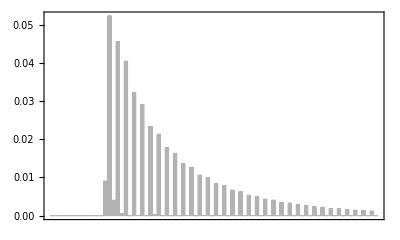
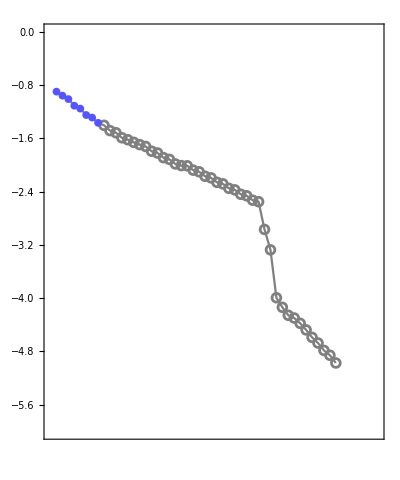
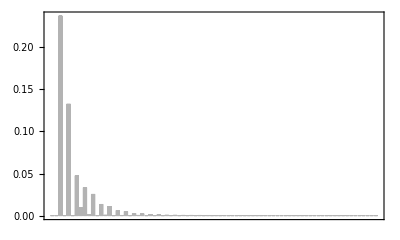
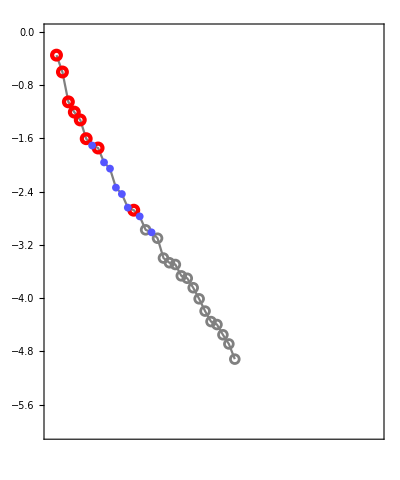
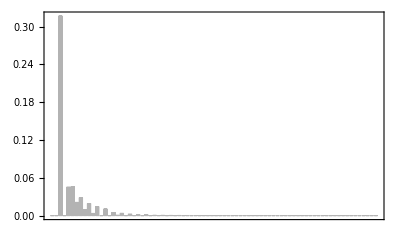
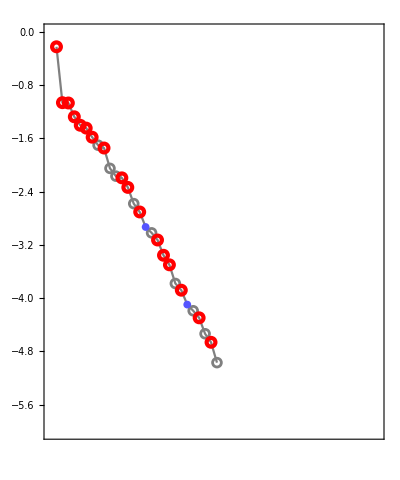
|  |  |  | 
 | (a)  Original  (f_(0, i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |  |  |  | 
 | (b)  Fertilization type 1  (f_(1, i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |  |  |  | 
 | (c)  Fertilization type 2  (f_(2, i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |        Species ordered by competitiveness |  |  | Rank

```mathematica
gt1=Grid[{
{Spacer[{0,0}]},{"",Item[fstylopt["(a)  Original  (f_(0, i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[inifredis,FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],
Show[gtts[0],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},

{Spacer[{0,0}]},{"",Item[fstylopt["(b)  Fertilization type 1  (f_(1, i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[endfredis[1],FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],Show[gtts[20],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},

{Spacer[{0,0}]},{"",Item[fstylopt["(c)  Fertilization type 2  (f_(2, i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[endfredis[2],FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],
Show[gtts[21],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},
{"",Item[fstylopt["       Species ordered by competitiveness",14]],Spacer[{0,0}],"",
Item[fstylopt["Rank ",14]]
}
},Alignment->Bottom]
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_equil.pdf"],gt1];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

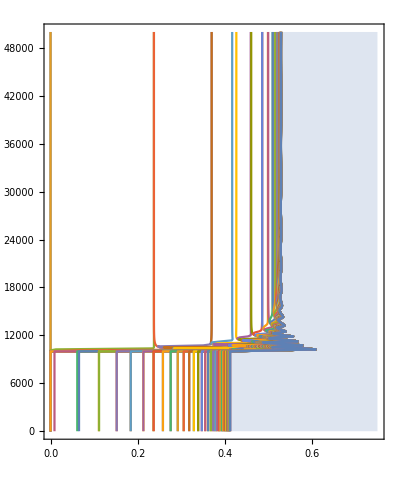
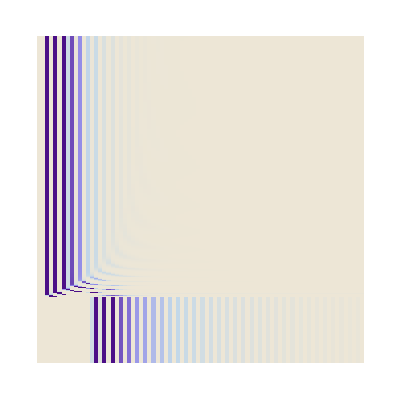
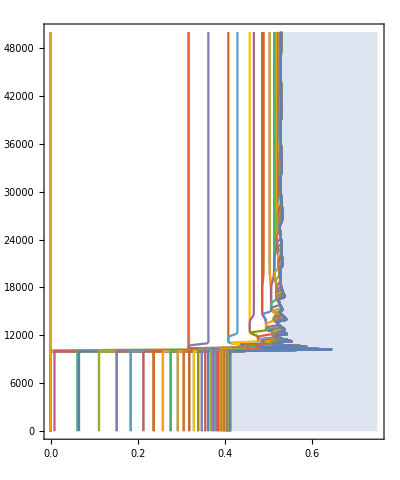
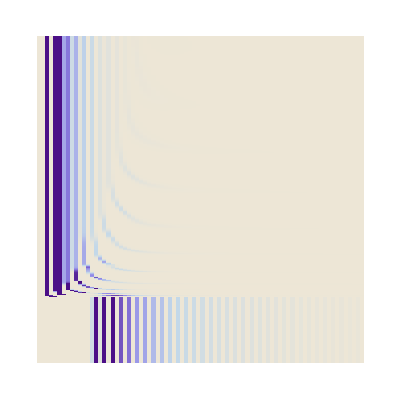
|  |  | 
 | (a)  Fertilization type 1  (f_(0, i) → f_(1, i)) |  | 
 |  |  | 
Time | -Graphics- | -Graphics- | 
 |  |  | 
 | (b)  Fertilization type 2  (f_(0, i) → f_(2, i)) |  | 
 |  |  | 
Time | -Graphics- | -Graphics- | 
 | Cumulative frequencies          | Species ordered by competitiveness |

```mathematica
gt2=Grid[{
{Spacer[{0,0}]},
{"",Item[fstylopt["(a)  Fertilization type 1  (f_(0, i) → f_(1, i))",15],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Time",14],Pi/2],Alignment->Center],ref1s[1],apta[1][[1]],""},
{Spacer[{0,0}]},
{"",Item[fstylopt["(b)  Fertilization type 2  (f_(0, i) → f_(2, i))",15],Alignment->Left]},
{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Time",14],Pi/2],Alignment->Center],ref1s[2],apta[2][[1]],leg1[2]},
{"",
Item[fstylopt["Cumulative frequencies"<>StringRepeat[" ",9],14],Alignment->Right],fstylopt["Species ordered by competitiveness",14]}
},Alignment->Bottom];

Print[gt2]
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_freq.pdf"],gt2];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

Number of detectable species : 49    Number of non-origina species : 0

Number of detectable species : 53    Number of non-origina species : 19

Number of detectable species : 47    Number of non-origina species : 17

Number of detectable species : 44    Number of non-origina species : 16

Number of detectable species : 45    Number of non-origina species : 16

Number of detectable species : 39    Number of non-origina species : 14

Number of detectable species : 45    Number of non-origina species : 16

Number of detectable species : 40    Number of non-origina species : 15

Number of detectable species : 41    Number of non-origina species : 14

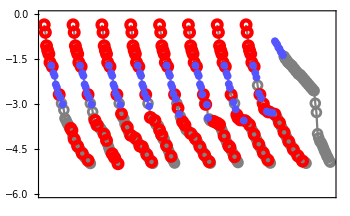

```mathematica
minlogs=-5;

ttno=9;
tinterval=10000;
For[ti=1,ti≤ttno,ti++,
For[i=1,i≤ino,i++,p[i]=ps1[[i]][tchange+(ti-1)tinterval]];
RADdraw[ti,minlogs];
];

shiftlen=-25;
grad1=Show[gtts[1],Table[Graphics[Translate[gtts[ttype][[1]],{(ttype-1)*shiftlen,0}]],{ttype,2,ttno}],PlotRange->{minlogs-1,gmax},Axes->None,ImageSize->350]
```

Number of detectable species : 49    Number of non-origina species : 0

Number of detectable species : 66    Number of non-origina species : 23

Number of detectable species : 19    Number of non-origina species : 11

Number of detectable species : 61    Number of non-origina species : 22

Number of detectable species : 41    Number of non-origina species : 18

Number of detectable species : 46    Number of non-origina species : 19

Number of detectable species : 33    Number of non-origina species : 16

Number of detectable species : 44    Number of non-origina species : 18

Number of detectable species : 36    Number of non-origina species : 17

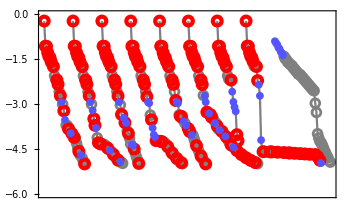

```mathematica
minlogs=-5;

ttno=9;
tinterval=10000;
For[ti=1,ti≤ttno,ti++,
For[i=1,i≤ino,i++,p[i]=ps2[[i]][tchange+(ti-1)tinterval]];
RADdraw[ti,minlogs];
];

shiftlen=-25;
grad2=Show[gtts[1],Table[Graphics[Translate[gtts[ttype][[1]],{(ttype-1)*shiftlen,0}]],{ttype,2,ttno}],PlotRange->{minlogs-1,gmax},Axes->None,ImageSize->350]
```

```mathematica
gt3=Grid[{
{Spacer[{0,0}]},
{"",Item[fstylopt["(a)  Fertilization type 1  (f_(0, i) → f_(1, i))",15],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2],Alignment->Center],grad1},
{Spacer[{0,0}]},
{"",Item[fstylopt["(b)  Fertilization type 2  (f_(0, i) → f_(2, i))",15],Alignment->Left]},
{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2],Alignment->Center],grad2}
},Alignment->Bottom]
```

| 
 | (a)  Fertilization type 1  (f_(0, i) → f_(1, i))
 | 
Log_10[Relative abundance] | -Graphics-
 | 
 | (b)  Fertilization type 2  (f_(0, i) → f_(2, i))
 | 
Log_10[Relative abundance] | -Graphics-

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_temp_change.pdf"],gt3];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

### Initial frequency

```mathematica
inita
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0.00904409},{15,0.0522965},{16,0.00401709},{17,0.0455568},{18,0.000443707},{19,0.0404316},{20,0},{21,0.0321276},{22,0.000020698},{23,0.0290703},{24,0},{25,0.0232806},{26,0.000219259},{27,0.0213179},{28,0},{29,0.0177652},{30,0},{31,0.0163046},{32,0},{33,0.0135731},{34,0.0000417535},{35,0.0126234},{36,0},{37,0.0105963},{38,0.0000299897},{39,0.00990213},{40,0},{41,0.00836115},{42,0.0000227546},{43,0.00784196},{44,0},{45,0.00665121},{46,0.0000172137},{47,0.00625583},{48,0},{49,0.00532285},{50,0.0000137179},{51,0.00501748},{52,0},{53,0.00428029},{54,0.0000105969},{55,0.00404178},{56,0},{57,0.00345403},{58,8.71915×10^-6},{59,0.00326606},{60,0},{61,0.0027957},{62,6.75167×10^-6},{63,0.0026465},{64,0},{65,0.0022675},{66,5.70478×10^-6},{67,0.00214838},{68,0},{69,0.00184285},{70,4.36937×10^-6},{71,0.00174731},{72,0},{73,0.00149941},{74,3.79946×10^-6},{75,0.00142249},{76,0},{77,0.00122184},{78,2.84151×10^-6},{79,0.00115971},{80,0}}

```mathematica
tahist[0]
```

{{15,0.126932},{17,0.110574},{19,0.0981342},{21,0.0779791},{23,0.0705583},{25,0.0565057},{27,0.051742},{29,0.0431191},{31,0.0395739},{33,0.0329442},{35,0.0306391},{37,0.0257189},{39,0.0240341},{14,0.0219515},{41,0.0202939},{43,0.0190337},{45,0.0161436},{47,0.0151839},{49,0.0129194},{51,0.0121782},{53,0.010389},{55,0.00981006},{16,0.00975013},{57,0.00838349},{59,0.00792726},{61,0.00678563},{63,0.0064235},{65,0.00550359},{67,0.00521448},{69,0.0044729},{71,0.004241},{73,0.00363933},{75,0.00345261},{77,0.0029656},{79,0.00281481},{18,0.00107695},{26,0.000532176},{34,0.000101343},{38,0.00007279},{42,0.0000552292},{22,0.0000502374},{46,0.0000417804},{50,0.0000332957},{54,0.0000257203},{58,0.0000211628},{62,0.0000163874},{66,0.0000138464},{70,0.0000106052}}

### Final frequencies type 1

```mathematica
endta1
```

{{1,0},{2,0},{3,0.237169},{4,0},{5,0.132444},{6,0},{7,0.0471044},{8,0.00954092},{9,0.0330154},{10,0.00110826},{11,0.0251714},{12,0},{13,0.0131676},{14,0.00056208},{15,0.0104015},{16,0},{17,0.00579692},{18,0.000105133},{19,0.00467371},{20,0},{21,0.00242163},{22,0.000179874},{23,0.00194022},{24,0},{25,0.00121192},{26,0},{27,0.000894645},{28,0},{29,0.000514831},{30,4.15555×10^-6},{31,0.000420333},{32,0},{33,0.000211606},{34,0.0000211952},{35,0.00016933},{36,0},{37,0.000114331},{38,0},{39,0.0000757631},{40,0},{41,0.0000516381},{42,0},{43,0.0000337516},{44,0},{45,0.0000234823},{46,0},{47,0.0000148807},{48,0},{49,0.0000108338},{50,0},{51,6.40278×10^-6},{52,0},{53,5.15106×10^-6},{54,0},{55,2.59364×10^-6},{56,2.60769×10^-7},{57,2.07621×10^-6},{58,0},{59,1.40366×10^-6},{60,0},{61,9.28958×10^-7},{62,0},{63,6.34642×10^-7},{64,0},{65,4.13469×10^-7},{66,0},{67,2.891×10^-7},{68,0},{69,1.81846×10^-7},{70,0},{71,1.33839×10^-7},{72,0},{73,7.77709×10^-8},{74,2.20886×10^-10},{75,6.36333×10^-8},{76,0},{77,3.14488×10^-8},{78,3.5951×10^-9},{79,2.50965×10^-8},{80,0}}

```mathematica
tahist[20]
```

{{3,0.448678},{5,0.250558},{7,0.0891123},{9,0.0624587},{11,0.0476195},{13,0.0249105},{15,0.0196775},{8,0.0180496},{17,0.0109666},{19,0.00884175},{21,0.00458125},{23,0.00367051},{25,0.00229271},{10,0.00209662},{27,0.00169249},{14,0.00106335},{29,0.00097396},{31,0.000795189},{33,0.000400318},{22,0.000340286},{35,0.000320339},{37,0.000216291},{18,0.000198891},{39,0.000143329},{41,0.0000976892},{43,0.0000638514},{45,0.0000444239},{34,0.0000400971},{47,0.0000281515},{49,0.0000204955},{51,0.0000121128}}

### Final frequencies type 2

```mathematica
endta2
```

{{1,0},{2,0},{3,0.316752},{4,0},{5,0.045303},{6,0.0457906},{7,0.0209482},{8,0.0280805},{9,0.0095355},{10,0.0189912},{11,0.00339493},{12,0.0138627},{13,0},{14,0.010513},{15,0},{16,0.00471419},{17,0.000619887},{18,0.00360197},{19,0},{20,0.00244077},{21,0},{22,0.0013917},{23,0},{24,0.00104293},{25,0},{26,0.000506326},{27,0.0000422992},{28,0.000395368},{29,0},{30,0.000233001},{31,0},{32,0.000167425},{33,0},{34,0.0000878106},{35,2.66195×10^-6},{36,0.0000695698},{37,0},{38,0.0000341613},{39,2.61164×10^-6},{40,0.0000267503},{41,0},{42,0.0000154169},{43,0},{44,0.000011469},{45,0},{46,5.6738×10^-6},{47,4.03763×10^-7},{48,4.44922×10^-6},{49,0},{50,2.52034×10^-6},{51,0},{52,1.92362×10^-6},{53,0},{54,9.09966×10^-7},{55,9.4622×10^-8},{56,7.07557×10^-7},{57,0},{58,4.44487×10^-7},{59,0},{60,2.90088×10^-7},{61,0},{62,1.78298×10^-7},{63,0},{64,1.20358×10^-7},{65,0},{66,7.00732×10^-8},{67,0},{68,5.1351×10^-8},{69,0},{70,2.60725×10^-8},{71,1.3765×10^-9},{72,2.05419×10^-8},{73,0},{74,1.09361×10^-8},{75,2.23807×10^-10},{76,8.68756×10^-9},{77,0},{78,4.11045×10^-9},{79,4.2683×10^-10},{80,3.19626×10^-9}}

```mathematica
tahist[21]
```

{{3,0.599233},{6,0.086627},{5,0.0857045},{8,0.0531229},{7,0.0396299},{10,0.0359276},{12,0.0262255},{14,0.0198886},{9,0.0180393},{16,0.00891834},{18,0.00681423},{11,0.00642254},{20,0.00461746},{22,0.00263284},{24,0.00197302},{17,0.00117271},{26,0.00095787},{28,0.000747959},{30,0.000440792},{32,0.000316736},{34,0.000166121},{36,0.000131612},{27,0.0000800218},{38,0.0000646266},{40,0.0000506064},{42,0.0000291657},{44,0.0000216971},{46,0.0000107337}}